```mathematica
3
```

```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]]
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3+ⅈ (y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3)

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

```mathematica
imaginary = (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7);
real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
```

```mathematica
FullSimplify[real+ⅈ imaginary - map3[x,y,μ]]
```

0

```mathematica
mat = {{D[real,x],D[real,y]},{D[imaginary,x],D[imaginary,y]}};
mat2 ={{D[D[real,x],x],D[D[real,y],y]},{D[D[imaginary,x],x],D[D[imaginary,y],y]}};
```

```mathematica
autovj = Eigenvalues[mat];
autovh = Eigenvalues[mat2];
eigenvecj = Eigensystem[mat];
eigenvech = Eigensystem[mat2]
```

{{0,2 μ^3 (-1-μ+6 x μ-6 x^2 μ-6 y μ+12 x y μ+6 y^2 μ-μ^2+6 x μ^2-6 x^2 μ^2-6 y μ^2+12 x y μ^2+6 y^2 μ^2+6 x μ^3-36 x^2 μ^3+60 x^3 μ^3-30 x^4 μ^3-6 y μ^3+72 x y μ^3-180 x^2 y μ^3+120 x^3 y μ^3+36 y^2 μ^3-180 x y^2 μ^3+180 x^2 y^2 μ^3+60 y^3 μ^3-120 x y^3 μ^3-30 y^4 μ^3-6 x^2 μ^4+40 x^3 μ^4-90 x^4 μ^4+84 x^5 μ^4-28 x^6 μ^4+12 x y μ^4-120 x^2 y μ^4+360 x^3 y μ^4-420 x^4 y μ^4+168 x^5 y μ^4+6 y^2 μ^4-120 x y^2 μ^4+540 x^2 y^2 μ^4-840 x^3 y^2 μ^4+420 x^4 y^2 μ^4+40 y^3 μ^4-360 x y^3 μ^4+840 x^2 y^3 μ^4-560 x^3 y^3 μ^4-90 y^4 μ^4+420 x y^4 μ^4-420 x^2 y^4 μ^4-84 y^5 μ^4+168 x y^5 μ^4+28 y^6 μ^4)},{{1,1},{-((-1-μ+6 x μ-6 x^2 μ+6 y^2 μ-μ^2+6 x μ^2-6 x^2 μ^2+6 y^2 μ^2+6 x μ^3-36 x^2 μ^3+60 x^3 μ^3-30 x^4 μ^3+36 y^2 μ^3-180 x y^2 μ^3+180 x^2 y^2 μ^3-30 y^4 μ^3-6 x^2 μ^4+40 x^3 μ^4-90 x^4 μ^4+84 x^5 μ^4-28 x^6 μ^4+6 y^2 μ^4-120 x y^2 μ^4+540 x^2 y^2 μ^4-840 x^3 y^2 μ^4+420 x^4 y^2 μ^4-90 y^4 μ^4+420 x y^4 μ^4-420 x^2 y^4 μ^4+28 y^6 μ^4)/(2 (-1+2 x) y μ (3+3 μ+3 μ^2-30 x μ^2+30 x^2 μ^2-30 y^2 μ^2-6 x μ^3+48 x^2 μ^3-84 x^3 μ^3+42 x^4 μ^3-20 y^2 μ^3+140 x y^2 μ^3-140 x^2 y^2 μ^3+42 y^4 μ^3))),1}}}

```mathematica
n=8;
L={};
For[i=38 300.,i≤ 384 30,i++,
μ=i/3000.;
For[j=1,j<10,j++,
x0=RandomReal[];
y0=RandomReal[] 10^-1;
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,y0}}];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,-y0}}];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
]
]
L = DeleteDuplicates[L];
Clear[μ]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPointPlot3D[L,ViewPoint->{0,0,Infinity},AxesLabel->{μ,x,y}];
ListPointPlot3D[L,AxesLabel->{μ,x,y}]
```

-Graphics3D-

```mathematica
tab1=FindRoot[{Re[map3[x,y,3.80]]== x,Im[map3[x,y,3.80]]== y},{{x,0.7},{y,0.1}}];
tab1⟦2,2⟧;
Round[tab1⟦2,2⟧10^8] 10^-8;
```

```mathematica
Lnum = {}
For[i=1,i<Length[L],i++,
AppendTo[Lnum,{L⟦i⟧,i}];]
(*AppendTo[Lnum⟦i⟧,i]]*)
```

{}

```mathematica
Length[Lnum]
Length[L]
```

723

724

```mathematica
Lnum⟦720⟧
```

{{3.84,0.169434,0.},720}

```mathematica
afterw = Select[L,#⟦1⟧>3.8284 &];
beforew= Select[L, #⟦1⟧<3.8284 &];
```

```mathematica
ListPointPlot3D[beforew];
```

```mathematica
pontos = L;
groupA = Select[pontos, #⟦2⟧<0.1 &];
groupBstep = Select[pontos, #⟦2⟧>0.1 &];
groupB = Select[groupBstep, #⟦2⟧<0.2 &];
groupCstep = Select[pontos, #⟦2⟧>0.4 &];
groupC= Select[groupCstep, #⟦2⟧<0.6 &];
groupDstep = Select[pontos, #⟦2⟧>0.6 &];
groupD = Select[groupDstep, #⟦2⟧<0.8 &];
groupE = Select[pontos, #⟦2⟧>0.8 &];
```

```mathematica
groupE⟦1,1⟧
```

3.8

8000

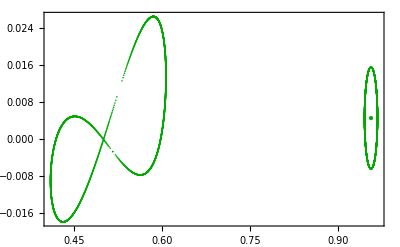

```mathematica
Block[{μ = 3.8},
list1 = {};
For[j=-1,j<1,j=j+0.001,
x=groupE⟦1,2⟧-10^-2 √(1-j^2)11/10;
y=groupE⟦1,3⟧+10^-2(j 11/10);
AppendTo[list1,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupE⟦1,2⟧+10^-2 √(1-j^2)11/10;
y=groupE⟦1,3⟧+10^-2(j 11/10);
AppendTo[list1,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
]
];
Length[list1]
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Green]],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> All]
```

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Green]],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{0.94,1},{0,-0.01}}]
```

-Graphics-

```mathematica
groupB⟦1,3⟧
```

0.016016

8000

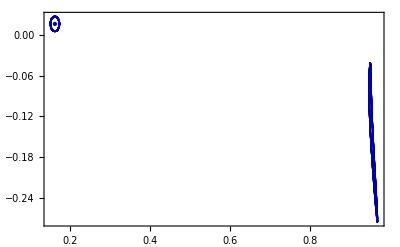

```mathematica
Block[{μ = 3.8},
list2 = {};
For[j=-1,j<1,j=j+0.001,
x=groupB⟦1,2⟧+10^-2 √(1-j^2)11/10;
y=groupB⟦1,3⟧+10^-2(j 11/10);
AppendTo[list2,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list2,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupB⟦1,2⟧-10^-2 √(1-j^2)11/10;
y=groupB⟦1,3⟧+10^-2(j 11/10);
AppendTo[list2,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list2,{x, y}],i=5]
]
]
];
Length[list2]
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Darker[Blue]],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],PlotRange-> All]
```

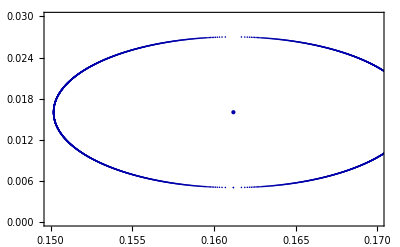

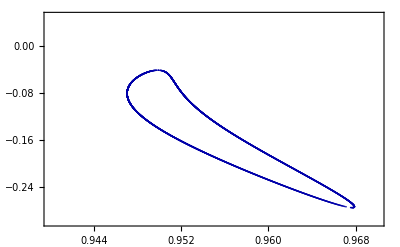

```mathematica
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Darker[Blue]],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],PlotRange-> {{0.15,0.17},{0,0.03}}]
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Darker[Blue]],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],PlotRange-> {{0.94,0.97},{-0.3,0.05}}]
```

8000

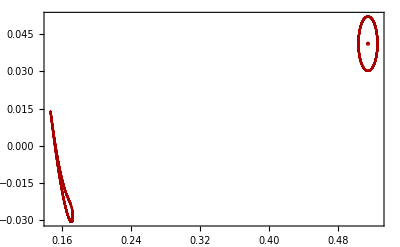

```mathematica
Block[{μ = 3.8},
list3 = {};
For[j=-1,j<1,j=j+0.001,
x=groupC⟦1,2⟧+10^-2 √(1-j^2)11/10;
y=groupC⟦1,3⟧+ 10^-2(j 11/10);
AppendTo[list3,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list3,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupC⟦1,2⟧-10^-2 √(1-j^2)11/10;
y=groupC⟦1,3⟧+10^-2(j 11/10);
AppendTo[list3,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list3,{x, y}],i=5]
]
]
];
Length[list3]
Show[ListPlot[list3,Frame->True,Joined->False,PlotStyle->Darker[Red]],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],PlotRange-> All]
```

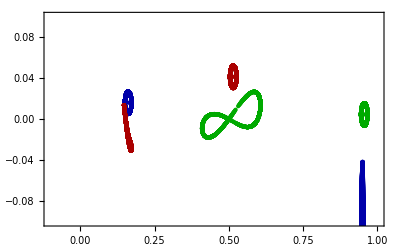

```mathematica
mu38=Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Green]}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Red]}],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{-0.1,1},{-0.1,0.1}}]
```

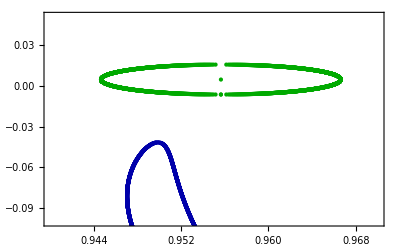

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Green]}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Red]}],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{0.94,0.97},{-0.1,0.051}}]
```

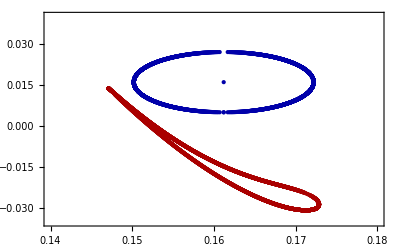
```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Green]}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Red]}],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{0.14,0.18},{-0.035,0.04}}]
-Graphics-
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Green]}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Red]}],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{0.4,0.6},{-0.05,0.05}}]
```

-Graphics-

-Graphics-

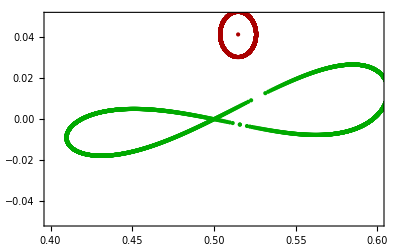

```mathematica
Length[groupE]
groupE⟦98⟧
```

156

{3.82167,0.956157,0.00221556}

8000

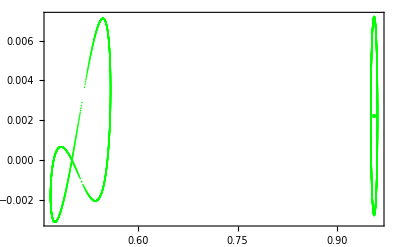

```mathematica
Block[{μ = groupE⟦98,1⟧},
list1 = {};
For[j=-1,j<1,j=j+0.001,
x=groupE⟦98,2⟧+10^-2 √(1-j^2)1/2;
y=groupE⟦98,3⟧+10^-2(j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupE⟦98,2⟧-10^-2 √(1-j^2)1/2;
y=groupE⟦98,3⟧+10^-2(j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
]
];
Length[list1]
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->{Green}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> All]
```

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->{Green}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> {{0.95,0.96},{0,-0.01}}]
```

-Graphics-

```mathematica
N[groupE⟦98,1⟧-groupB⟦117,1⟧,20]
```

0.001

```mathematica
groupB⟦117,1⟧
```

3.82067

8000

8000

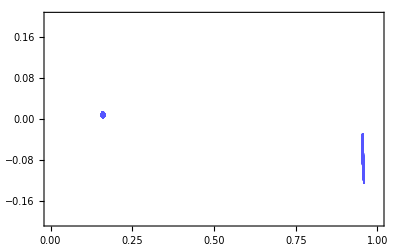

```mathematica
Block[{μ = groupB⟦117,1⟧},
list2 = {};
For[j=-1,j<1,j=j+0.001,
x=groupB⟦117,2⟧+10^-2 √(1-j^2)1/2;
y=groupB⟦117,3⟧+10^-2(j 1/2);
AppendTo[list2,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^3,AppendTo[list2,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupB⟦117,2⟧-10^-2 √(1-j^2)1/2;
y=groupB⟦117,3⟧+10^-2(j 1/2);
AppendTo[list2,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^3,AppendTo[list2,{x, y}],i=5]
]
]
];
Length[list2]
8000
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Lighter[Blue]],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧}]}],PlotRange-> {{0,1},{-0.2,0.2}}]
```

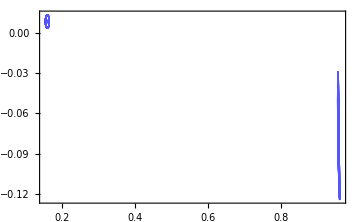

-Graphics-

```mathematica
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Lighter[Blue]],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧}]}],PlotRange-> {{0.154,0.165},{0,-0.015}},ImageSize-> Medium]
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Lighter[Blue]],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧}]}],PlotRange-> {{0.95,0.965},{0.15,0}},ImageSize-> Medium]
```

```mathematica
groupB⟦117,1⟧
```

3.82067

```mathematica
N[groupB⟦117,1⟧-groupC⟦115,1⟧,20]
```

0.00133333

8000

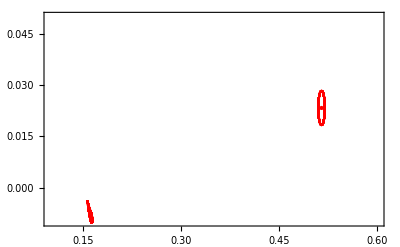

```mathematica
Block[{μ = groupC⟦115,1⟧},
list3 = {};
For[j=-1,j<1,j=j+0.001,
x=groupC⟦115,2⟧+10^-2 √(1-j^2)1/2;
y=groupC⟦115,3⟧+10^-2(j 1/2);
AppendTo[list3,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list3,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupC⟦115,2⟧-10^-2 √(1-j^2)1/2;
y=groupC⟦115,3⟧+10^-2(j 1/2);
AppendTo[list3,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list3,{x, y}],i=5]
]
]
];
Length[list3]
Show[ListPlot[list3,Frame->True,Joined->False,PlotStyle->Red],Graphics[{Red,PointSize[Large],Point[{groupC⟦115,2⟧,groupC⟦115,3⟧}]}],PlotRange-> {{0.1,0.6},{-0.01,0.05}}]
```

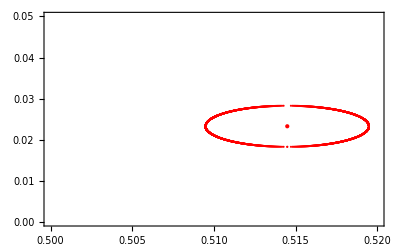

```mathematica
Show[ListPlot[list3,Frame->True,Joined->False,PlotStyle->Red],Graphics[{Red,PointSize[Large],Point[{groupC⟦115,2⟧,groupC⟦115,3⟧}]}],PlotRange-> {{0.5,0.52},{0,0.05}}]
```

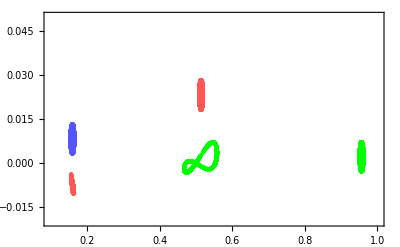

```mathematica
mu38233=Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Green}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Red]}],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧}]}],Graphics[{Lighter[Red],PointSize[Large],Point[{groupC⟦115,2⟧,groupC⟦115,3⟧}]}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> {{0.1,1},{-0.02,0.05}}]
```

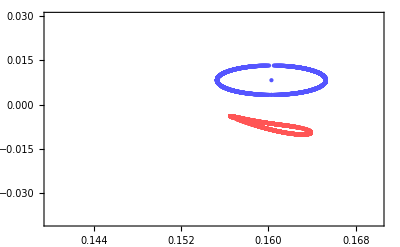

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Green}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Red]}],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧}]}],Graphics[{Lighter[Red],PointSize[Large],Point[{groupC⟦115,2⟧,groupC⟦115,3⟧}]}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> {{0.14,0.17},{-0.04,0.03}}]
```

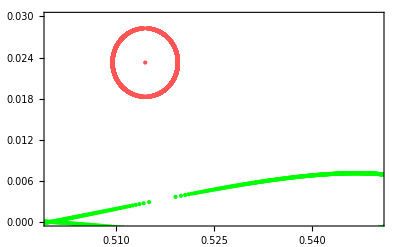

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Green}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Red]}],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧}]}],Graphics[{Lighter[Red],PointSize[Large],Point[{groupC⟦115,2⟧,groupC⟦115,3⟧}]}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],
PlotRange-> {{0.5,0.55},{0,0.03}}]
```

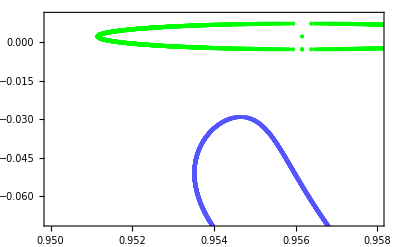

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Green}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Red]}],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧}]}],Graphics[{Lighter[Red],PointSize[Large],Point[{groupC⟦115,2⟧,groupC⟦115,3⟧}]}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> {{0.95,0.958},{-0.07,0.01}}]
```

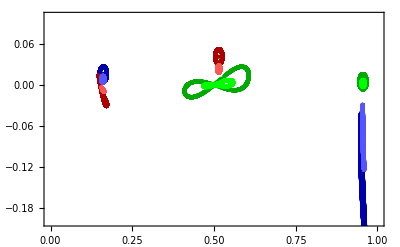

```mathematica
Show[mu38,mu38233,PlotRange-> {{0,1},{-0.2,0.1}}]
```

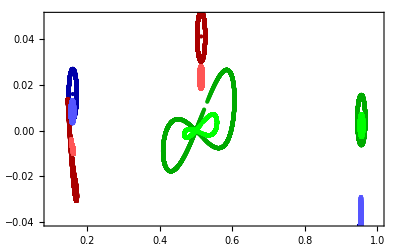

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.1,1},{-0.04,0.05}}]
```

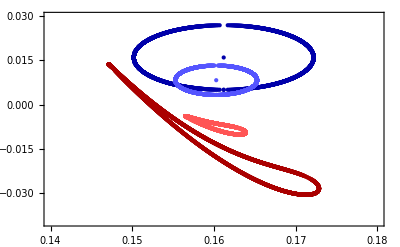

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.14,0.18},{-0.04,0.03}}]
```

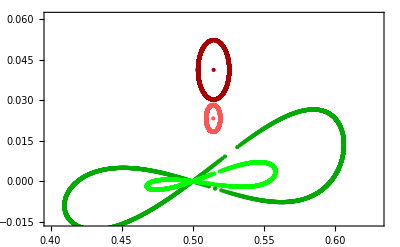

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.4,0.63},{-0.015,0.061}}]
```

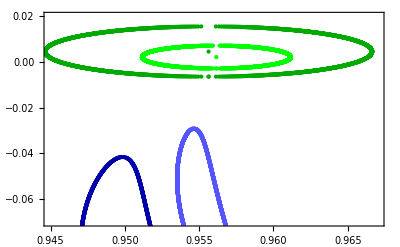

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.945,0.967},{-0.07,0.02}}]
```